```mathematica
Clear["Global`*"]
(*name="student@10.0.1.9://home/student/BEM/Kramer2021_0d03/result.json"*)
data01DLPF4=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/LPF4/01D_LPF4.txt"}],"Data"];
data03DLPF4=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/LPF4/03D_LPF4.txt"}],"Data"];
%[[1]]
data01DFNPF1=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/FNPF1/01D_FNPF1.txt"}],"Data"];
data03DFNPF1=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/FNPF1/03D_FNPF1.txt"}],"Data"];
%[[1]]
data01DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/01D_CI95_Normalized.txt"}],"Data"];
%[[1]]
data03DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/03D_CI95_Normalized.txt"}],"Data"];
%[[1]]
data05DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/05D_Measured1_Normalized.txt"}],"Data"];
%[[1]]
name="~/BEM/Kramer2021_H00d03_small_ALE3/result.json"
(*name="~/BEM/Kramer2021_H00d03_ALE3/result.json"*)
Quiet[Z=(data="float_COM"/.Import[name])[[;;,3]];];
Quiet[Vx=(data="float_velocity"/.Import[name])[[;;,1]];];
Quiet[Vy=(data="float_velocity"/.Import[name])[[;;,2]];];
Quiet[Vz=(data="float_velocity"/.Import[name])[[;;,3]];];
Quiet[time="simulation_time"/.Import[name];];
(*Kramer20210d03=Import[NotebookDirectory[]<>"Kramer2021_0d3.csv"];*)
H0=30/1000;
jsonInfo[imported_]:=Grid[Join[{{"no.","title","data length"}},Table[{i,imported[[i]][[1]],Length[imported[[i]][[2]]]},{i,1,Min[10,Length[imported]]}]],Frame->All,Background->{None,{LightGray,{LightMagenta,Magenta}}}];
jsonInfo[Import[name,"JSON"]]

imported=Import[name];
getData[var_,n_:0]:=If[n>0,(var/.imported)[[;;,n]],var/.imported];
importGetData[name_,var_,n_:0]:=With[{imported=Import[name]},If[n>0,(var/.imported)[[;;,n]],var/.imported]];
```

{t [s],,x3 [m]}

{t [s],,x3 [m]}

{t/Te0 [-],,x3/H_{0,m} (mean) [-],,Lower 95% CI bound [-],,Upper 95% CI bound [-]}

{t/Te0 [-],,x3/H_{0,m} (mean) [-],,Lower 95% CI bound [-],,Upper 95% CI bound [-]}

{t/Te0 [-],,x3/H_{0,m} [-],,WG1/H_{0,m} [-],,WG2/H_{0,m} [-],,WG3/H_{0,m} [-]}

~/BEM/Kramer2021_H00d03_small_ALE3/result.json

no. | title | data length
1 | cpu_time | 701
2 | float_COM | 701
3 | float_EK | 701
4 | float_EP | 701
5 | float_accel | 701
6 | float_area | 701
7 | float_force | 701
8 | float_pitch | 701
9 | float_roll | 701
10 | float_torque | 701

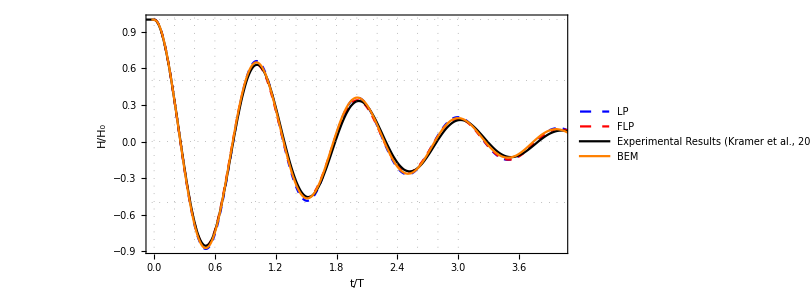
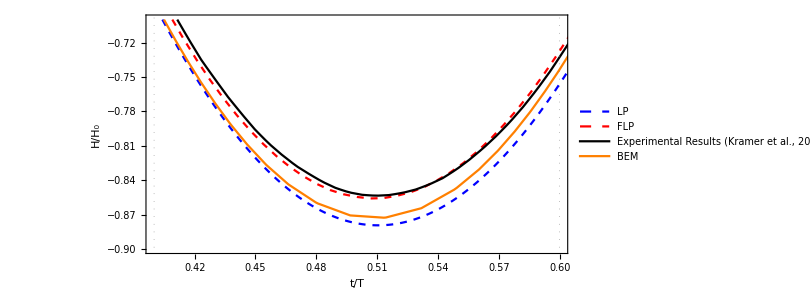
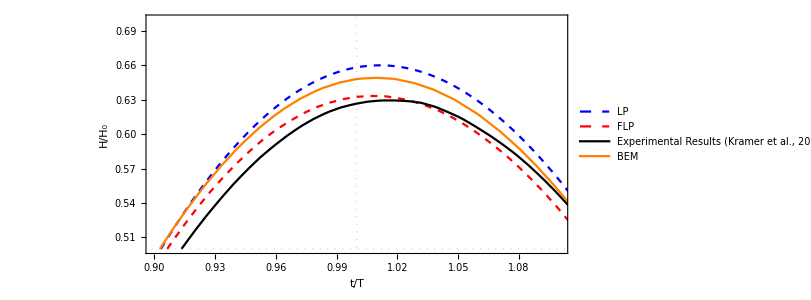
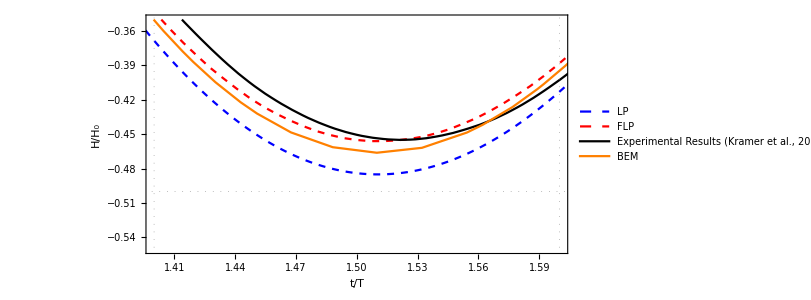
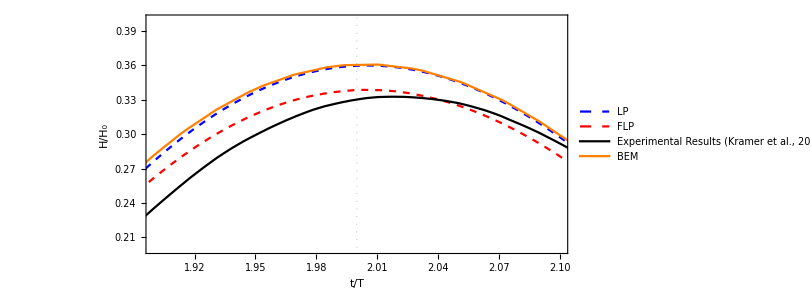

```mathematica
T=0.76;

fig=Table[
ListPlot[
{{#1/T,#2/H0}&@@@data01DLPF4[[2;;]],
{#1/T,#2/H0}&@@@data01DFNPF1[[2;;]],
{#1,#2(*/H0*)}&@@@data01DMeasured1Raw[[2;;]],
{(importGetData[name,"simulation_time"]-0.02)/T,(importGetData[name,"float_COM",3]-((*-34.8+*)900)/1000)/H0}ᵀ
(*,{#1/0.76,#2/H0}&@@@data01DFNPF1[[2;;]]
,{#1/0.76,#2/H0}&@@@data01DLPF4[[2;;]]*)
},
Joined->{True,True},
PlotStyle->{{Blue,Dashed},{Red,Dashed},{Black},{Orange}},
BaseStyle->{FontFamily->"Times"},
PlotRange->ranges,
AspectRatio->1/2,
GridLines->{Table[i,{i,0.,3.,0.2}],Table[i,{i,-1.,1.,0.5}]},
Frame->True,
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["H/H_0",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
ImageSize->600,
PlotLegends->LineLegend[{"LP","FLP","Experimental Results (Kramer et al., 2021)","BEM"},LegendMarkerSize->20,LabelStyle->15]
],
{ranges,{{{0,4.},All},
{{0.5-0.1,0.5+0.1},{-0.8-0.1,-0.8+0.1}},
{{1-0.1,1+0.1},{0.6-0.1,0.6+0.1}},
{{1.5-0.1,1.5+0.1},{-0.45-0.1,-0.45+0.1}},
{{2-0.1,2+0.1},{0.3-0.1,0.3+0.1}}}}
]
```

```mathematica
(*dir="/Users/tomoaki/Library/CloudStorage/Dropbox/meeting/海洋工学シンポジウム/2023/投稿論文/"*)
dir=NotebookDirectory[];
r=200
Export[dir<>"HH0_vs_tT_Kramer2012.jpg",fig,ImageResolution->r];
Export[dir<>"HH0_vs_tT_Kramer2012.png",fig,ImageResolution->r];
Export[dir<>"HH0_vs_tT_Kramer2012.pdf",fig];
Export[dir<>"HH0_vs_tT_Kramer2012.eps",fig];
Export[dir<>"HH0_vs_tT_Kramer2012.jpeg",fig,ImageResolution->r];
```

200

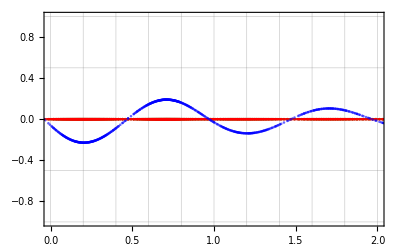

```mathematica
ListPlot[
{
{(time-0.05)/0.76,Vx}ᵀ,
{(time-0.05)/0.76,Vy}ᵀ,
{(time-0.05)/0.76,Vz}ᵀ
},
PlotStyle->{{Darker[Green],Opacity[0.6]},{Red},{Dashed,Blue,Opacity[0.6]},{Thick}},
Joined->{False,True,True,True},
PlotRange->{{0,2},{-1.,1.}},
PlotTheme->"Scientific",
Frame->True,
Mesh->All,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]}
]
```